3.83001

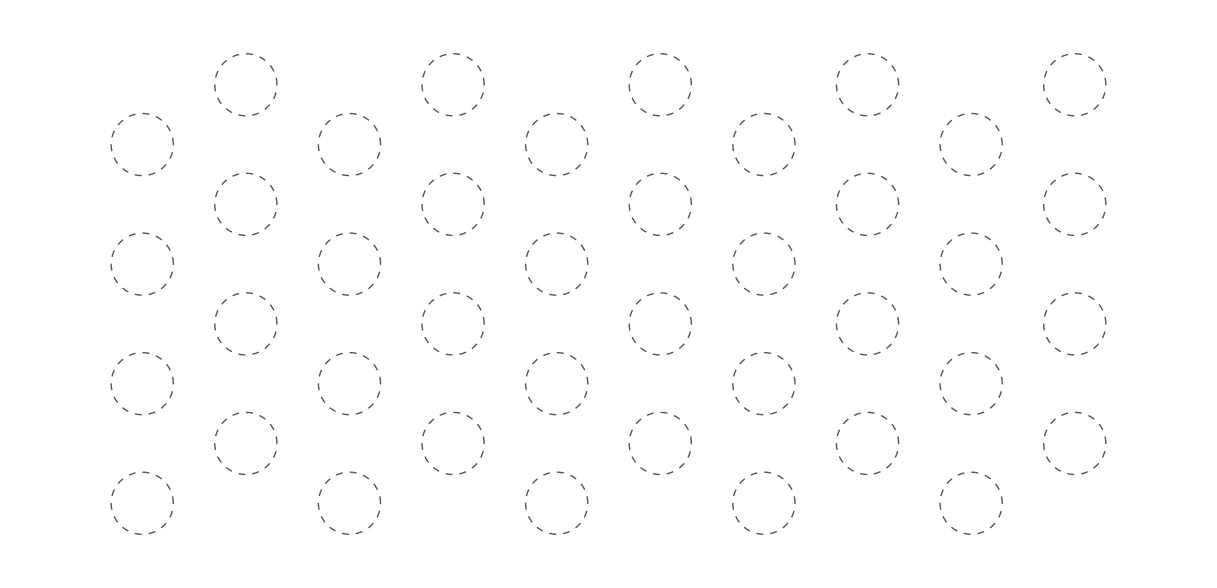

2mer.png

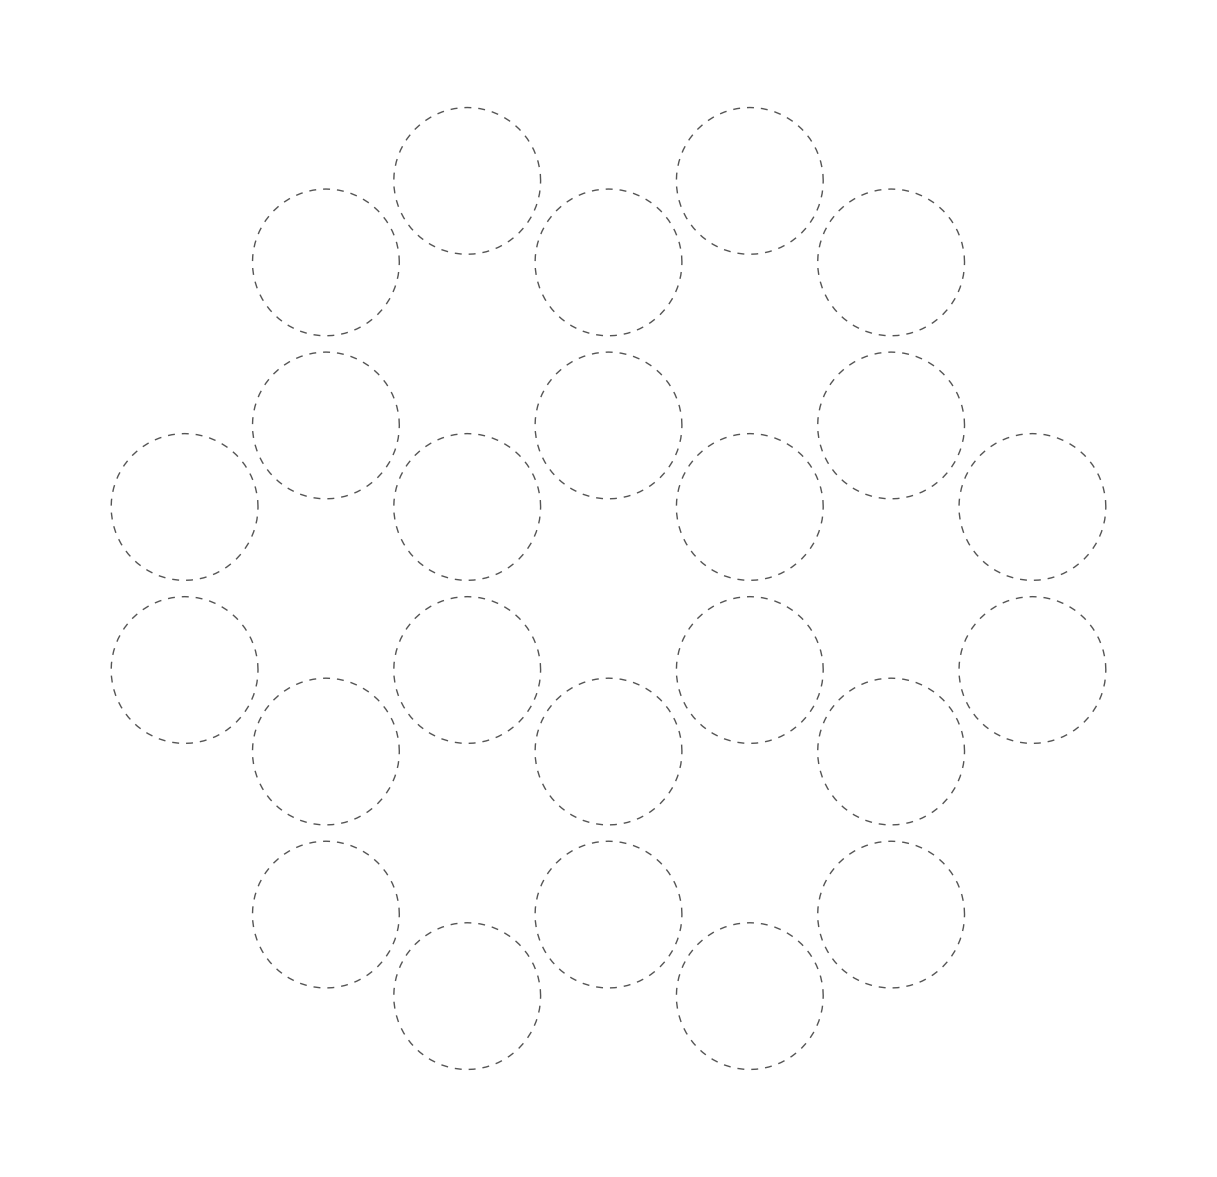

```mathematica
ClearAll["Global`*"]
Subscript[m, e]=9.10938291*10^(-31); (*Kg*) ch=1.602176565*10^(-19); (*C*) ℏ=1.054571726*10^(-34); (*J·s*)
Subscript[ℏ, eV]=6.58211928*10^(−16);(*eV·s*) c=2.99*10^(8); (*m^2·s^-2*) ev=1.602176565*10^(-19); (*J*)
Subscript[m, e,eV]=Subscript[m, e]*c^2/ev; (*MeV·c^2*) ϵ0=8.85418782*10^(-12); (*C^2·N^-1·m^-2*) nm=10^(-9); (*m*)
(*Metal parameters*)
ϵd=1; ϵinf=3.77; (*no dimensions, Relative permittivity*) a0=7*nm; ℏωp=9.2; (*eV*)  ωp=ℏωp/Subscript[ℏ, eV];
 ωsp=ωp/Sqrt[ϵinf+2*ϵd]; αsp=4*π*ϵ0*a0^3*(3/(ϵinf+2));
m=ch^2/(αsp*ωsp^2); ℏωsp=ℏ*ωsp/ch
(*Geometry*)
d0=4*nm; r0=(2+d0/a0)//N; (*Coupling*) g0=αsp/(4*π*ϵ0*a0^3*r0^3);
e1=Sqrt[3]/2; e2=1; e3=(1/2); r={x,y,z} ; id={{1,0,0},{0,1,0},{0,0,1}};


numPart = 24;
Loc={{0,e2,0},{e1,e3,0},{e1,-e3,0},{0,-e2,0},{-e1,-e3,0},{-e1,e3,0},{0,2 e2,0},{e1,5 e3,0},{2 e1,4 e3,0},{2 e1,2 e3,0},{3 e1,e3,0},{3 e1,-e3,0},{2 e1,-2 e3,0},{2 e1,-4 e3,0},{e1,-5 e3,0},{0,-2 e2,0},{-e1,-5 e3,0},{-2 e1,-4 e3,0},{-2 e1,-2 e3,0},{-3 e1,-e3,0},{-3 e1,e3,0},{-2 e1,2 e3,0},{-2 e1,4 e3,0},{-e1,5 e3,0}};

Test=Flatten[Table[{{3*n,Sqrt[3]*m},{3*n+3/2,Sqrt[3]*m+Sqrt[3]/2}},{n,0,4},{m,0,3}],2];
CrcsTest=Table[Graphics[{Thick,Dashed,Darker[Gray],Circle[Test[[j]],0.45]}],{j,1,Length[Test]}];
Show[CrcsTest]
(*Loc={{0,e1,0},{0,-e1,0},{0,-3*e1,0}};*)

Loc2D=Table[Delete[Loc[[j]],3],{j,1,numPart}];

Pnts=Point[Loc2D];

Crcs=Table[Graphics[{Thick,Dashed,Darker[Gray],Circle[Flatten[Loc2D[[j]]],0.45]}],{j,1,numPart}];
Crcs2=Table[Graphics[{Thickness[0.008],Black,Circle[Flatten[Loc2D[[j]]],0.45]}],{j,1,numPart}];
G1=Graphics[{Opacity[0.2],PointSize[0.17],Yellow,Pnts}];
G2=Show[Crcs];
G3=Graphics[Line[Join[Loc2D,{Loc2D[[1]]}]]];
G4=Graphics[Line[{Loc2D[[1]],Loc2D[[numPart]]}]];
Export["2mer.png",G2]
Gfin=Show[Crcs]
Rloc[n_]:=r-Loc[[n]];
```

(1)
 |  |  |  |

True

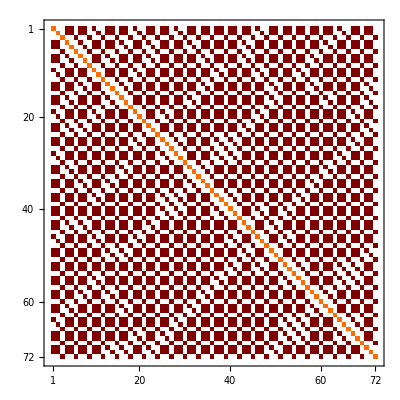

```mathematica
FullM0=IdentityMatrix[3*numPart];
R[n_,m_]:=(Rloc[n]-Rloc[m]);
NormR[n_,m_]:=Norm[R[n,m]];
nUnit[n_,m_]:=R[n,m]/NormR[n,m];



T1[n_,m_]:=id/NormR[n,m]^(3);
T2[n_,m_]:=-3*Outer[Times,nUnit[n,m],nUnit[n,m]]/NormR[n,m]^(3);


Coupling[n_,m_]:=(g)*(T1[n,m]+T2[n,m])[[1;;3,1;;3]];


F1=Do[If[n≠m  && Norm[R[n,m]]≥1 ,FullM0[[3*n-2;;3*n,3*m-2;;3*m]]=Coupling[n,m]],{n,1,numPart},{m,1,numPart}];

F3=FullM0;
F2=FullM0

SymmetricMatrixQ[F2]
MatrixPlot[F2]
```

```mathematica
g=g0;
EigSys2=Eigensystem[F2];
Table[ Sqrt[EigSys2[[1]][[m]]],{m,1,3*numPart}]
Table[ Sqrt[EigSys2[[1]][[m]]],{m,1,3*numPart}];
```

{1.06528,1.06456,1.06108,1.05615,1.05615,1.0523,1.0523,1.04101,1.03993,1.03993,1.03983,1.03983,1.03925,1.03925,1.03283,1.02918,1.0249,1.02487,1.02366,1.02366,1.02329,1.02329,1.0232,1.0232,1.02235,1.02025,1.01556,1.01556,1.01157,1.01074,1.01022,1.01022,1.00797,1.00797,1.00155,1.00155,0.995,0.995,0.988201,0.987949,0.987949,0.986791,0.986791,0.98431,0.983094,0.983094,0.982855,0.980722,0.977441,0.977028,0.977028,0.976082,0.975928,0.975928,0.971028,0.971028,0.970715,0.970715,0.968423,0.96651,0.965061,0.962653,0.962653,0.960953,0.960953,0.940893,0.936849,0.936849,0.934583,0.934583,0.932587,0.931905}

```mathematica
map=Import["/Users/cherqui/Documents/colormap.dat","Table"];
MB=Function[Blend[RGBColor@@@ map,#1]];
```